```mathematica
SetOptions[EvaluationNotebook[],StyleDefinitions->Notebook[{Cell[StyleData[StyleDefinitions->"Default.nb"]],Cell[StyleData["Graphics",All],FontFamily->"CMU Serif"]},StyleDefinitions->"PrivateStylesheetFormatting.nb"]]
```



```mathematica
(*benchmarklist={3,4,5,7,8,10,11};*)
ColorData[24,"Image"]
(*ColorData[109,"Image"]*)
colorselecitonumber=24;
```

```mathematica
energygrid=Grid[{Table[Style[If[j==1,{"(√s= 3,","6,","10,","14,","30,","100 TeV)"}[[i]],"TeV"],If[j≠0,ColorData[colorselecitonumber][i]],Bold],{j,1,2,1},{i,1,6,1}][[1]]},Spacings->{0.5,0}]
```

(√s= 3, | 6, | 10, | 14, | 30, | 100 TeV)

```mathematica
SetDirectory[NotebookDirectory[]];
<<CustomTicks`
ww0m1 = Import["ww0m1_partonic.dat","List"];
ww01 = Import["ww01_partonic.dat","List"];
ww10 = Import["ww10_partonic.dat","List"];
wwm10 = Import["wwm10_partonic.dat","List"];
ww00 = Import["ww00_partonic.dat","List"];
dytw00 = Import["ww00_partonic_dyt015_linear.dat","List"];
dytw11 = Import["ww11_partonic_dyt015_linear.dat","List"];
dytwm1m1 = Import["wwm1m1_partonic_dyt015_linear.dat","List"];
mdytw00 = Import["ww00_partonic_dytm015_linear.dat","List"];
mdytw11 = Import["ww11_partonic_dytm015_linear.dat","List"];
mdytwm1m1 = Import["wwm1m1_partonic_dytm015_linear.dat","List"];
```

```mathematica
ww11 = Import["ww11_partonic.dat","List"];
wwm1m1 = Import["wwm1m1_partonic.dat","List"];
ww1m1 = Import["ww1m1_partonic.dat","List"];
wwm11 = Import["wwm11_partonic.dat","List"];
sqrtsList=Table[350+25*i,{i,0,400}];
```

```mathematica
zz0m1 = Import["zz0m1_partonic.dat","List"];
zz01 = Import["zz01_partonic.dat","List"];
zz10 = Import["zz10_partonic.dat","List"];
zzm10 = Import["zzm10_partonic.dat","List"];
zz00 = Import["zz00_partonic.dat","List"];
```

```mathematica
dytz00 = Import["zz00_partonic_dyt015_linear.dat","List"];
dytz11 = Import["zz11_partonic_dyt015_linear.dat","List"];
dytzm1m1 = Import["zzm1m1_partonic_dyt015_linear.dat","List"];
mdytz00 = Import["zz00_partonic_dytm015_linear.dat","List"];
mdytz11 = Import["zz11_partonic_dytm015_linear.dat","List"];
mdytzm1m1 = Import["zzm1m1_partonic_dytm015_linear.dat","List"];
```

```mathematica
zz11 = Import["zz11_partonic.dat","List"];
zzm1m1 = Import["zzm1m1_partonic.dat","List"];
zz1m1 = Import["zz1m1_partonic.dat","List"];
zzm11 = Import["zzm11_partonic.dat","List"];
```

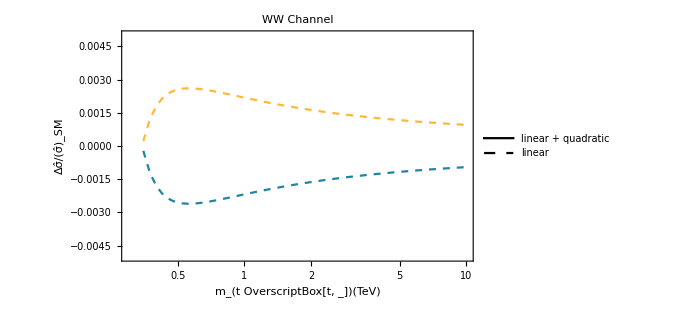

```mathematica
factor=0.3894*10^12;
linearlineplot=ListPlot[{Transpose[{sqrtsList/10^3,(dytw00+dytw11+dytwm1m1-ww00-ww11-wwm1m1)/(ww00+ww01+ww0m1+ww10+wwm10+ww11+wwm1m1+ww1m1+wwm11)}],Transpose[{sqrtsList/10^3,(mdytw00+mdytw11+mdytwm1m1-ww00-ww11-wwm1m1)/(ww00+ww01+ww0m1+ww10+wwm10+ww11+wwm1m1+ww1m1+wwm11)}]},Joined->True,PlotStyle->{Directive[ColorData[colorselecitonumber][6],Dashed],Directive[Dashed,ColorData[colorselecitonumber][2]]},Frame->True,BaseStyle->{FontFamily->"Times"},ScalingFunctions->{"Log",None},FrameLabel->{Style["m_(t OverscriptBox[t, _])(TeV)",Black,17,FontFamily->"Times"],Style["Δσ̂/(σ̂)_SM",Black,17,FontFamily->"Times"]},
PlotLabel->Style["WW Channel",Black,17],
PlotLegends->Placed[LineLegend[{Directive[Black],Directive[Black,Dashed]},{Style["linear + quadratic",FontFamily->"Times",15],Style["linear",FontFamily->"Times",15]}],{0.72,0.8}],
PlotRange->{{.300,10},{-0.005,0.005}},
FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},
FrameTicksStyle->Directive[Black,15],ImageSize->500]
(*customticks package*)
```

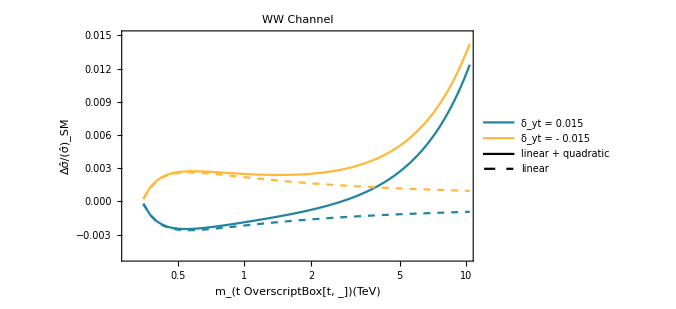

```mathematica
combined =Show[nonlinearlineplot,linearlineplot]
```

```mathematica
Export["combinedww.pdf",combined]
```

combinedww.pdf

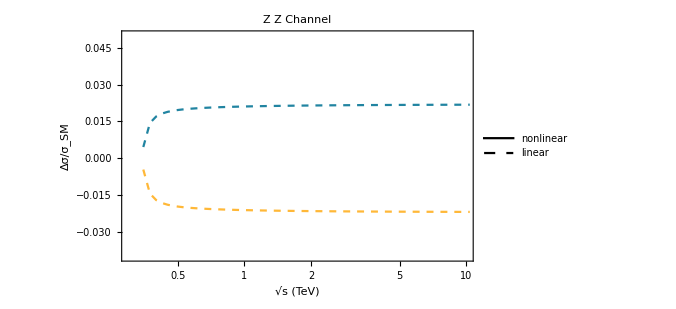

```mathematica
linearlineplot1=ListPlot[{Transpose[{sqrtsList/10^3,(dytz00+dytz11+dytzm1m1-zz00-zz11-zzm1m1)/(zz00+zz01+zz0m1+zz10+zzm10+zz11+zzm1m1+zz1m1+zzm11)}],Transpose[{sqrtsList/10^3,(mdytz00+mdytz11+mdytzm1m1-zz00-zz11-zzm1m1)/(zz00+zz01+zz0m1+zz10+zzm10+zz11+zzm1m1+zz1m1+zzm11)}]},ScalingFunctions->{"Log",None},Joined->True,PlotStyle->{Directive[ColorData[colorselecitonumber][6],Dashed],Directive[Dashed,ColorData[colorselecitonumber][2]]},Frame->True,BaseStyle->{FontFamily->"Times"},FrameLabel->{Style["\!\(\*SqrtBox[\(s\)]\) (TeV)",Black,25,FontFamily->"Times"],Style["Δσ/σ_SM",Black,25,FontFamily->"Times"]},
PlotLabel->Style["Z Z Channel",Black,22],
PlotLegends->Placed[LineLegend[{Directive[Black],Directive[Black,Dashed]},{Style["nonlinear",FontFamily->"Times",18],Style["linear",FontFamily->"Times",18]}],{0.72,0.8}],
PlotRange->{{.300,10},{-0.04,0.05}},FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},
FrameTicksStyle->Directive[Black,18],ImageSize->500]
```

```mathematica
combined1 =Show[nonlinearlineplot1,linearlineplot1]
```

Show::gcomb: Could not combine the graphics objects in Show[nonlinearlineplot1,].

Show[nonlinearlineplot1,-Graphics-]

```mathematica
Export["combinedzz.pdf",combined1]
```

combinedzz.pdf

```mathematica
ticks0=LogTicks[10,-2,6,TickLabelStep->2];
ticks1=ticks0;
Do[ticks1[[i,1]]=10^(ticks0[[i,1]]),{i,1,Length[ticks0]}]
ticks1;
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/ishmammahbub/Desktop/Research/Partonic Distribution/WWtt/Plot Partonic Distribution/untitled folder

```mathematica
(*Export["WW_partonic_dyt_linear.pdf",lineplot]
Export["ZZ_partonic_dyt_linear.pdf",lineplot1]
```

```mathematica
(dytw00-ww00)/(ww00+ww01+ww0m1+ww10+wwm10+ww11+wwm1m1+ww1m1+wwm11)
```

{-0.000238986,-0.00130936,-0.00191353,-0.00226352,-0.00246751,-0.0025841,-0.00264664,-0.00267495,-0.0026812,-0.0026731,-0.00265563,-0.0026321,-0.00260472,-0.00257501,-0.00254399,-0.00251238,-0.00248067,-0.00244921,-0.00241822,-0.00238786,-0.00235823,-0.0023294,-0.0023014,-0.00227424,-0.00224792,-0.00222244,-0.00219778,-0.00217392,-0.00215083,-0.0021285,-0.00210688,-0.00208595,-0.00206569,-0.00204608,-0.00202707,-0.00200865,-0.00199079,-0.00197347,-0.00195667,-0.00194036,-0.00192453,-0.00190914,-0.00189419,-0.00187966,-0.00186553,-0.00185177,-0.00183839,-0.00182536,-0.00181266,-0.0018003,-0.00178824,-0.00177648,-0.00176502,-0.00175383,-0.0017429,-0.00173224,-0.00172183,-0.00171165,-0.0017017,-0.00169198,-0.00168247,-0.00167317,-0.00166407,-0.00165517,-0.00164645,-0.00163791,-0.00162954,-0.00162135,-0.00161332,-0.00160545,-0.00159773,-0.00159016,-0.00158274,-0.00157545,-0.00156831,-0.00156129,-0.0015544,-0.00154764,-0.001541,-0.00153447,-0.00152806,-0.00152176,-0.00151556,-0.00150947,-0.00150349,-0.0014976,-0.00149181,-0.00148611,-0.00148051,-0.00147499,-0.00146956,-0.00146422,-0.00145895,-0.00145377,-0.00144867,-0.00144364,-0.00143869,-0.00143381,-0.00142901,-0.00142427,-0.0014196,-0.001415,-0.00141046,-0.00140598,-0.00140157,-0.00139722,-0.00139292,-0.00138869,-0.00138451,-0.00138038,-0.00137631,-0.0013723,-0.00136833,-0.00136442,-0.00136055,-0.00135674,-0.00135297,-0.00134925,-0.00134557,-0.00134194,-0.00133836,-0.00133481,-0.00133131,-0.00132785,-0.00132443,-0.00132105,-0.00131771,-0.00131441,-0.00131115,-0.00130792,-0.00130473,-0.00130157,-0.00129845,-0.00129537,-0.00129232,-0.0012893,-0.00128631,-0.00128336,-0.00128043,-0.00127754,-0.00127468,-0.00127184,-0.00126904,-0.00126627,-0.00126352,-0.0012608,-0.00125811,-0.00125545,-0.00125281,-0.0012502,-0.00124761,-0.00124505,-0.00124251,-0.00124,-0.00123751,-0.00123505,-0.00123261,-0.00123019,-0.00122779,-0.00122542,-0.00122307,-0.00122074,-0.00121843,-0.00121614,-0.00121387,-0.00121162,-0.0012094,-0.00120719,-0.001205,-0.00120283,-0.00120068,-0.00119855,-0.00119644,-0.00119434,-0.00119226,-0.0011902,-0.00118816,-0.00118613,-0.00118412,-0.00118213,-0.00118015,-0.00117819,-0.00117625,-0.00117432,-0.00117241,-0.00117051,-0.00116863,-0.00116676,-0.0011649,-0.00116307,-0.00116124,-0.00115943,-0.00115763,-0.00115585,-0.00115408,-0.00115233,-0.00115058,-0.00114885,-0.00114714,-0.00114543,-0.00114374,-0.00114206,-0.0011404,-0.00113874,-0.0011371,-0.00113547,-0.00113385,-0.00113224,-0.00113065,-0.00112906,-0.00112749,-0.00112592,-0.00112437,-0.00112283,-0.0011213,-0.00111978,-0.00111827,-0.00111677,-0.00111528,-0.00111381,-0.00111234,-0.00111088,-0.00110943,-0.00110799,-0.00110656,-0.00110514,-0.00110373,-0.00110232,-0.00110093,-0.00109955,-0.00109817,-0.0010968,-0.00109545,-0.0010941,-0.00109276,-0.00109142,-0.0010901,-0.00108878,-0.00108748,-0.00108618,-0.00108488,-0.0010836,-0.00108232,-0.00108106,-0.0010798,-0.00107854,-0.0010773,-0.00107606,-0.00107483,-0.00107361,-0.00107239,-0.00107118,-0.00106998,-0.00106879,-0.0010676,-0.00106642,-0.00106524,-0.00106408,-0.00106291,-0.00106176,-0.00106061,-0.00105947,-0.00105834,-0.00105721,-0.00105609,-0.00105497,-0.00105386,-0.00105276,-0.00105166,-0.00105057,-0.00104948,-0.00104841,-0.00104733,-0.00104626,-0.0010452,-0.00104415,-0.00104309,-0.00104205,-0.00104101,-0.00103998,-0.00103895,-0.00103792,-0.00103691,-0.00103589,-0.00103489,-0.00103388,-0.00103289,-0.0010319,-0.00103091,-0.00102993,-0.00102895,-0.00102798,-0.00102701,-0.00102605,-0.00102509,-0.00102414,-0.00102319,-0.00102225,-0.00102131,-0.00102038,-0.00101945,-0.00101852,-0.0010176,-0.00101669,-0.00101578,-0.00101487,-0.00101397,-0.00101307,-0.00101218,-0.00101129,-0.0010104,-0.00100952,-0.00100864,-0.00100777,-0.0010069,-0.00100604,-0.00100518,-0.00100432,-0.00100347,-0.00100262,-0.00100177,-0.00100093,-0.00100009,-0.000999261,-0.000998432,-0.000997606,-0.000996784,-0.000995965,-0.000995151,-0.00099434,-0.000993532,-0.000992728,-0.000991928,-0.000991131,-0.000990338,-0.000989548,-0.000988761,-0.000987978,-0.000987199,-0.000986423,-0.00098565,-0.00098488,-0.000984114,-0.000983351,-0.000982591,-0.000981835,-0.000981082,-0.000980332,-0.000979585,-0.000978841,-0.0009781,-0.000977363,-0.000976628,-0.000975897,-0.000975168,-0.000974443,-0.000973721,-0.000973001,-0.000972285,-0.000971571,-0.00097086,-0.000970153,-0.000969448,-0.000968746,-0.000968046,-0.00096735,-0.000966656,-0.000965966,-0.000965277,-0.000964592,-0.000963909,-0.000963229,-0.000962552,-0.000961877,-0.000961205,-0.000960536,-0.000959869,-0.000959205,-0.000958543,-0.000957884,-0.000957228,-0.000956574,-0.000955922,-0.000955273,-0.000954627,-0.000953983,-0.000953341,-0.000952702,-0.000952065,-0.000951431,-0.000950799,-0.000950169,-0.000949542,-0.000948917,-0.000948294,-0.000947674,-0.000947056,-0.00094644,-0.000945826,-0.000945215,-0.000944606}